## VertexCut

```mathematica
VertexCut[g_?UndirectedGraphQ,parm___]:=VertexCut[DirectedGraph[g],parm]
```

```mathematica
VertexCut[g_?MultigraphQ,parm___]:=VertexCut[SimpleGraph[g],parm]
```

```mathematica
VertexCut[g:Except[_?LoopFreeGraphQ],parm___]:=VertexCut[SimpleGraph[g],parm]
```

```mathematica
VertexCut[g_?DirectedGraphQ]:=
Block[{res,n,m,a,b,u,v},
n=VertexCount[g];(*I understand this line*)
m=Transpose[IncidenceMatrix[g]];(*I don't understand what this line is for I understand what the incidence matrix represents and what the transpose of a matrix represents but I don't understand what this does.*)
a=UnitStep[m-1];(*remove negative values from directed edges/arcs.*)
b=a-m;(*constraints*)
res=LinearOptimization[-Total[u+v](*I understand this objective function and the linear optimization*),{u+v \[VectorLessEqual]1(*I understand this as saying *),a.u +b.v\[VectorLessEqual]1,a.v +b.u\[VectorLessEqual]1,Total[u]\[VectorGreaterEqual]1,Total[v]\[VectorGreaterEqual]1,u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0,u\[VectorLessEqual]1,v\[VectorLessEqual]1},{u∈Vectors[n,Integers],v∈Vectors[n,Integers]}];
VertexList[g][[Flatten[Position[Total[{u,v} /. res],0]]]] 
]
```

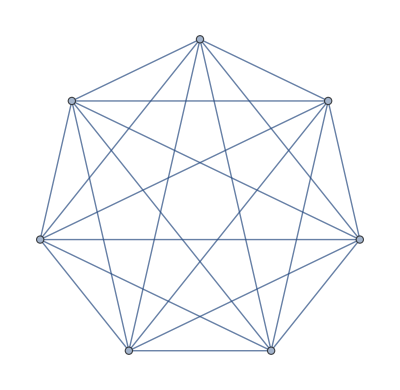

```mathematica
RandomGraph[{7,21}]
```

```mathematica
IncidenceMatrix[RandomGraph[{7,21}]]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1)

```mathematica
Transpose@IncidenceMatrix[RandomGraph[{7,21}]]//MatrixForm
```

(1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1)

#### Undirected Graph

```mathematica
Transpose@IncidenceMatrix[RandomGraph[{7,21}]]//Normal
```

{{1,1,0,0,0,0,0},{1,0,1,0,0,0,0},{1,0,0,1,0,0,0},{1,0,0,0,1,0,0},{1,0,0,0,0,1,0},{1,0,0,0,0,0,1},{0,1,1,0,0,0,0},{0,1,0,1,0,0,0},{0,1,0,0,1,0,0},{0,1,0,0,0,1,0},{0,1,0,0,0,0,1},{0,0,1,1,0,0,0},{0,0,1,0,1,0,0},{0,0,1,0,0,1,0},{0,0,1,0,0,0,1},{0,0,0,1,1,0,0},{0,0,0,1,0,1,0},{0,0,0,1,0,0,1},{0,0,0,0,1,1,0},{0,0,0,0,1,0,1},{0,0,0,0,0,1,1}}

```mathematica
UnitStep[Transpose@IncidenceMatrix[RandomGraph[{7,21}]]-1]//Normal
```

{{1,1,0,0,0,0,0},{1,0,1,0,0,0,0},{1,0,0,1,0,0,0},{1,0,0,0,1,0,0},{1,0,0,0,0,1,0},{1,0,0,0,0,0,1},{0,1,1,0,0,0,0},{0,1,0,1,0,0,0},{0,1,0,0,1,0,0},{0,1,0,0,0,1,0},{0,1,0,0,0,0,1},{0,0,1,1,0,0,0},{0,0,1,0,1,0,0},{0,0,1,0,0,1,0},{0,0,1,0,0,0,1},{0,0,0,1,1,0,0},{0,0,0,1,0,1,0},{0,0,0,1,0,0,1},{0,0,0,0,1,1,0},{0,0,0,0,1,0,1},{0,0,0,0,0,1,1}}

#### Directed Graph

```mathematica
randomDirectedGraph=RandomGraph[{7,21},DirectedEdges->True]
```

-Graphics-

```mathematica
m=Transpose@IncidenceMatrix[randomDirectedGraph]//Normal
```

{{-1,0,0,1,0,0,0},{-1,0,0,0,0,1,0},{1,-1,0,0,0,0,0},{0,-1,1,0,0,0,0},{0,-1,0,1,0,0,0},{0,-1,0,0,1,0,0},{0,-1,0,0,0,1,0},{1,0,-1,0,0,0,0},{0,1,-1,0,0,0,0},{0,0,-1,0,1,0,0},{0,0,1,-1,0,0,0},{0,0,0,-1,1,0,0},{0,0,0,-1,0,0,1},{1,0,0,0,-1,0,0},{0,1,0,0,-1,0,0},{0,0,1,0,-1,0,0},{0,0,0,0,-1,1,0},{0,0,0,0,-1,0,1},{1,0,0,0,0,-1,0},{0,0,1,0,0,0,-1},{0,0,0,0,0,1,-1}}

```mathematica
a=UnitStep[Transpose@IncidenceMatrix[randomDirectedGraph]-1]//Normal
```

{{0,0,0,1,0,0,0},{0,0,0,0,0,1,0},{1,0,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,1,0},{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,0,0,1,0,0},{0,0,1,0,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,0,1},{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,1},{1,0,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,0,0,1,0}}

```mathematica
a-m
```

{{1,0,0,0,0,0,0},{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,1,0,0,0,0,0},{0,1,0,0,0,0,0},{0,1,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,1,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,1,0,0},{0,0,0,0,1,0,0},{0,0,0,0,1,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1}}

## Objective Cost Consideration

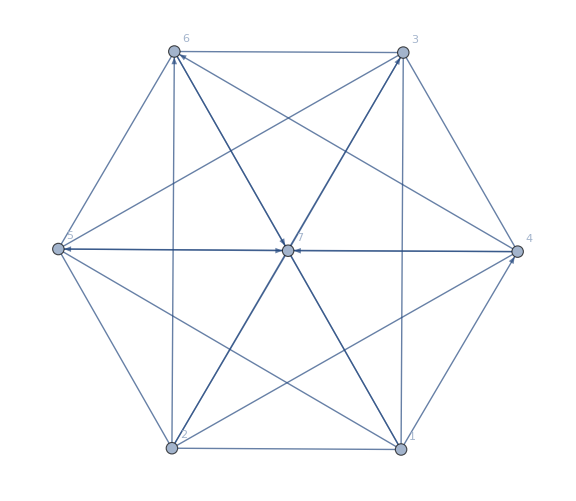

```mathematica
randomWeightedMixedGraph=Graph[UndirectedGraphToMixedGraph[RandomGraph[{7,21}],.5],EdgeWeight->RandomReal[ⅇ,21],VertexLabels->"Name"]
```

```mathematica
WeightedAdjacencyMatrix[randomWeightedMixedGraph]//MatrixForm
```

(0. | 1.53461 | 0.67037 | 1.96553 | 0.95353 | 1.11088 | 2.3371
0. | 0. | 0.470941 | 0.143719 | 1.00747 | 0.0214898 | 1.28253
0. | 0. | 0. | 1.48829 | 2.07787 | 0.0871885 | 2.17226
0. | 0.143719 | 1.48829 | 0. | 2.08556 | 0.365175 | 0.869437
0.95353 | 1.00747 | 2.07787 | 0. | 0. | 0.735799 | 2.21221
1.11088 | 0. | 0.0871885 | 0. | 0.735799 | 0. | 0.211643
2.3371 | 1.28253 | 2.17226 | 0. | 0. | 0. | 0.)

```mathematica
AnnotationValue[{randomWeightedMixedGraph,1->2},EdgeWeight]
```

$Failed

```mathematica
AnnotationValue[{randomWeightedMixedGraph,1<->6},EdgeWeight]
```

1.14076

```mathematica
Position[WeightedAdjacencyMatrix[randomWeightedMixedGraph]//Normal,AnnotationValue[{randomWeightedMixedGraph,1<->6},EdgeWeight]]
```

{{1,3}}

```mathematica
VertexList[randomWeightedMixedGraph]
```

{1,2,3,4,5,6,7}

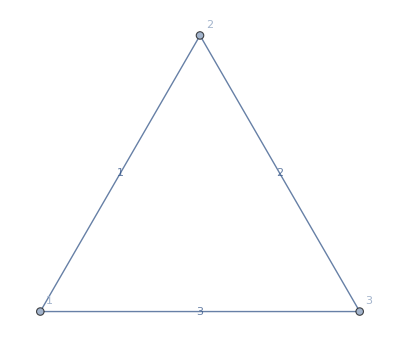

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeWeight->{1,2,3},VertexLabels->"Name",EdgeLabels->"EdgeWeight"]
```

```mathematica
WeightedAdjacencyMatrix[%]//MatrixForm
```

(0 | 1 | 3
1 | 0 | 2
3 | 2 | 0)

```mathematica
objective=cost Total[u+v]
```

```mathematica
secondConstraint=u+v \[VectorGreaterEqual]1
```

u+v\[VectorGreaterEqual]1

```mathematica
thirdConstraint=u\[VectorGreaterEqual]0
```

u\[VectorGreaterEqual]0

```mathematica
fourthConstraint=v\[VectorGreaterEqual]0
```

v\[VectorGreaterEqual]0

```mathematica
DirectedGraphArcs[RandomMixedGraph[{8,21},.5]]
```

{1->3,2->6,2->4,2->7,2->5,3->5,4->5,5->8,5->7,6->8}

### Simple Case

```mathematica
Block[{vertexCount,edgeData,formatDirectedEdgesData,edgeDifferenceData},vertexCount=VertexCount[randomWeightedMixedGraph];edgeData=Transpose[IncidenceMatrix[randomWeightedMixedGraph]];
formatDirectedEdgesData=UnitStep[edgeData-1];(*remove negative values from directed edges/arcs.*)
edgeDifferenceData=formatDirectedEdgesData-edgeData;(*constraints*)LinearOptimization[-Total[u+v](*I understand this objective function and the linear optimization*),{u+v \[VectorGreaterEqual]1(*I understand this as saying *),u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0},{u∈Vectors[vertexCount,Integers],v∈Vectors[vertexCount,Integers]}]
 ]
```

LinearOptimization::ubnd: The problem is unbounded.

{u→{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},v→{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}

```mathematica
LinearOptimization[-Total[u+v],{secondConstraint,thirdConstraint,fourthConstraint},{u∈Vectors[n,Integers],v∈Vectors[n,Integers]}]
```

LinearOptimization::varspec: u∈Vectors[n,] is not a valid variable specification.

LinearOptimization[-Total[u+v],{u+v\[VectorLessEqual]1,u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0},{u∈Vectors[n,ℤ],v∈Vectors[n,ℤ]}]

```mathematica
LinearOptimization[-objective,constraints,variables]
```

```mathematica
VertexCut[g_?DirectedGraphQ,s_,t_] /; VertexQ[g,s]&&VertexQ[g,t]:=
Block[{res,n,m,a,b,u,v,i,j},
n=VertexCount[g];
m=Transpose[IncidenceMatrix[g]];
a=UnitStep[m-1];
b=a-m;
i=VertexIndex[g,s];
j=VertexIndex[g,t];
res=LinearOptimization[-Total[u+v],{u+v \[VectorLessEqual]1,a.u +b.v\[VectorLessEqual]1,a.v +b.u\[VectorLessEqual]1,Total[u]\[VectorGreaterEqual]1,Total[v]\[VectorGreaterEqual]1,u\[VectorGreaterEqual]0,v\[VectorGreaterEqual]0,u\[VectorLessEqual]1,v\[VectorLessEqual]1,Indexed[u,i]==1,Indexed[u,j]==0,Indexed[v,i]==0,Indexed[v,j]==1},{u∈Vectors[n,Integers],v∈Vectors[n,Integers]}];
VertexList[g][[Flatten[Position[Total[{u,v} /. res],0]]]] 
]
```

```mathematica
VertexCut[RandomGraph[{5,10}]]
```

LinearOptimization::nsolc: There are no points that satisfy the constraints.

{}

## Example

```mathematica
edges={start->F201,F201->Q,start->F202,F202->Q,Q->P,start->F203,F203->P,P->B21,F203->B21,start->F204,F204->B21,start->F205,F205->B21,start->F206,F206->B21,start->F207,F207->C21,C211->C21,F207->C211,C212->C21,start->C213,C213->C21,C21->B21,B21->H21,C21->H21,H21->H211,start->FH211,FH211->H211,C211->H211,H211->IH2111,IH2111->goal,start->L21,L21->C21,B21->L21,C21->D1,C212->D1,B21->D1,D1->E22,C211->E22,start->FE22,FE22->E22,E22->E221,start->FE221,FE221->E221,E22->K3123,K3123->goal,E221->MR,MR->goal,B21->G21,start->FG21T1,FG21T1->G21,start->FG21T2,FG21T2->G21,G21->G211,G211->X,X->goal,B21->K31,C21->K31,C212->K31,K31->K3111,K3111->Y,Y->goal,B21->J31,C21->J31,C211->J31,start->FJ311,FJ311->J31,start->FJ312,FJ312->J31,J31->J311,J311->goal,B21->J32,C21->J32,C211->J32,start->FJ32,FJ32->J32,J32->J321,J321->goal,B21->R201,R201->Z,Z->goal,P->T1,F204->T1,F206->T1,T1->R201,R201->AQ,AQ->goal,T1->U1,F208->U1,U1->U11,U11->RE,RE->goal,T1->U2,F208->U2,U2->U21,U21->TY,TY->goal};
```

```mathematica
g=Graph[edges];
```

```mathematica
a=VertexCut[g,start,goal]
```

{B21,H211,E22,E221,G21,K3111,J31,J32,T1}

```mathematica
Length[a]
```

9

```mathematica
VertexConnectivity[g,start,goal]
```

9

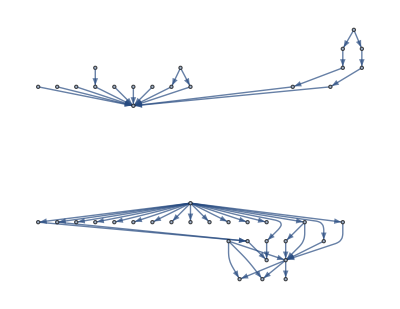

```mathematica
VertexDelete[g,a]
```